## ^6 Li_2 Potentials

MLR parameters in energy units of cm^-1 and length units of Å

#### X^1 Σ_g^+ State

```mathematica
SingletDe = 8516.709;
Singletre = 2.6729932;
Singletref = 3.85;
SingletC6 = 6.71527 * 10^6;
SingletC8 = 1.12588 * 10^8;
SingletC10 = 2.78604 * 10^9;
p = 5;
q = 3;
Singletβcf = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
SingletUcf = {0.19400, -0.0100, 0.390};

pad = 6;
qad = pad;
```

```mathematica
SingletUinf = 0;
```

#### a^3 Σ_u^+ State

```mathematica
TripletDe = 333.758;
Tripletre = 4.17005000;
Tripletref=8.0;
TripletC6 = 6.7185*10^6;
TripletC8 =1.12629*10^8;
TripletC10 = 2.78683*10^9;
Tripletβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
TripletUcf = {0.059};

ρ = 0.54;
```

```mathematica
TripletUinf = SingletUinf;
```

### Setup MLR potentials for reference isotope (i.e., ^7 Li)

#### X^1 Σ_g^+ State

```mathematica
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βfun[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
Singletulr[r_,c6_,c8_,c10_]:= c6/r^6+c8/r^8+c10/r^10;
Singletβinf=Log[(2 SingletDe)/Singletulr[Singletre,SingletC6,SingletC8,SingletC10]];
SingletVMLR[r_]:= SingletDe(1-Singletulr[r,SingletC6,SingletC8,SingletC10]/Singletulr[Singletre,SingletC6,SingletC8,SingletC10]*Exp[-βfun[r,Singletβcf,Singletβinf,y[Singletre,r,q],y[Singletref,r,p],y[Singletref,r,q]]*y[Singletre,r,p]])^2-SingletDe;
```

```mathematica
Asymptotic[SingletVMLR[r],r->∞]
```

-(6.71527×10^6)/r^6

#### a^3 Σ_u^+ State

```mathematica
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
```

```mathematica
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,ρ,-1];
```

```mathematica
Tripletulr[r_]:= DDSTriplet[6,r] TripletC6/r^6+DDSTriplet[8,r] TripletC8/r^8+DDSTriplet[10,r] TripletC10/r^10;
Tripletβinf=Log[(2 TripletDe)/Tripletulr[Tripletre]];
βTriplet[r_]:= Tripletβinf*y[Tripletref,r,5]+(1-y[Tripletref,r,5])*Sum[Tripletβcf[[j+1]]*y[Tripletref,r,3]^j,{j,0,Length[Tripletβcf]-1}];
TripletVMLR[r_]:= TripletDe(1-Tripletulr[r]/Tripletulr[Tripletre]*Exp[-βTriplet[r]*y[Tripletre,r,p]])^2-TripletDe;
```

```mathematica
Tripletulr[r]
```

(2.78683×10^9 (1-ⅇ^(-0.54 (0.33+0.0722327 r) r))^9)/r^10+(1.12629×10^8 (1-ⅇ^(-0.54 (0.4125+0.0807587 r) r))^7)/r^8+(6.7185×10^6 (1-ⅇ^(-0.54 (0.55+0.0932521 r) r))^5)/r^6

### Calculate ΔV_ad for the ^6 Li_2 Potentials

#### Define the masses for the lithium isotopes

```mathematica
Δm = massLi6-massLi7;
massfactor = (2 Δm)/massLi6;
```

```mathematica
amu = 1822.89;
massLi7 = 7.016004*amu;
massLi6 = 6.0151227950*amu;
massLi7/2
massLi6/2
```

6394.7

5482.45

#### Calculate the well-depths and equilibrium lengths for the a^3 Σ_u^+ and X^1 Σ_g^+ states of ^6 Li_2

```mathematica
SingletΔDe = massfactor(SingletUinf-SingletUcf[[1]])
TripletΔDe = massfactor (TripletUinf-TripletUcf[[1]])
```

0.0645609

0.0196345

```mathematica
Singlet6De = SingletDe+SingletΔDe
Triplet6De = TripletDe+TripletΔDe
```

8516.77

333.778

Well depths in Hartree

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
```

```mathematica
Singlet6DeH = Singlet6De*invcminHartree
Triplet6DeH=Triplet6De*invcminHartree
Singlet7DeH=SingletDe*invcminHartree
Triplet7DeH=TripletDe*invcminHartree
```

0.0388053

0.0015208

0.038805

0.00152071

```mathematica
Series[SingletVMLR[r],{r,Singletre,2}]
```

-8516.71-3.28496×10^-12 (r-2.67299)+6424.64 (r-2.67299)^2+O[r-2.67299]^3

```mathematica
Series[TripletVMLR[r],{r,Tripletre,2}]
```

-333.758-1.21067×10^-13 (r-4.17005)+222.679 (r-4.17005)^2+O[r-4.17005]^3

```mathematica
Singletkbar=6424.64*2;
Tripletkbar=222.679*2;
Stildeprime[ucf0_,ucf1_,uinf_,pad_,qad_,re_]:= ((uinf-ucf0)pad + ucf1 qad)/(2 re);
SingletΔre = -massfactor (1/Singletkbar Stildeprime[SingletUcf[[1]],SingletUcf[[2]],SingletUinf,pad,qad,Singletre])
TripletΔre = -massfactor (Stildeprime[TripletUcf[[1]],0,TripletUinf,pad,qad,Tripletre]/Tripletkbar)
```

-5.92984×10^-6

-0.0000317169

```mathematica
Singlet6re = Singletre + SingletΔre
Triplet6re = Tripletre+TripletΔre
```

2.67299

4.17002

```mathematica
Singlet6re*AngstrominBohr
Triplet6re*AngstrominBohr
```

5.05121

7.88019

#### Define adiabatic radial strength function

```mathematica
Stilde[r_,pad_,uinf_,ucf_,qad_,re_]:= y[re,r,pad] uinf +(1-y[re,r,pad]) Sum[ucf[[i+1]] y[re,r,qad]^i,{i,0,Length[ucf]-1}];
TripletΔVad[r_]:= massfactor*Stilde[r,pad,TripletUinf,TripletUcf,qad,Tripletre];
SingletΔVad[r_]:= massfactor*Stilde[r,pad,SingletUinf,SingletUcf,qad,Singletre];
```

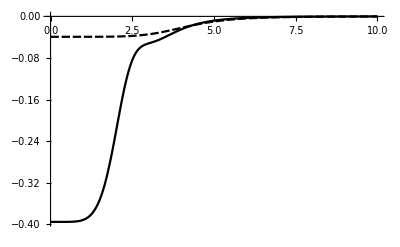

```mathematica
Plot[{SingletΔVad[r],TripletΔVad[r]},{r,0,10},PlotRange->Full]
```

```mathematica
Asymptotic[SingletΔVad[r],r->∞]
```

-139.347/r^6

### Setup MLR potentials for ^6 Li_2

```mathematica
Triplet6VMLR[r_]:= TripletVMLR[r]+TripletΔVad[r];
Singlet6VMLR[r_]:= SingletVMLR[r]+SingletΔVad[r];
```

```mathematica
Asymptotic[Singlet6VMLR[r],r->∞]
```

-(6.71541×10^6)/r^6

```mathematica
-(6.715409346814029*^6)/r^6
```

```mathematica
Asymptotic[Triplet6VMLR[r],r->∞]
```

-(6.71871×10^6)/r^6

```mathematica
Plot[{Singlet6VMLR[r],Triplet6VMLR[r]},{r,1.0,10},PlotRange->{-8750,1000}]
```

-Graphics-

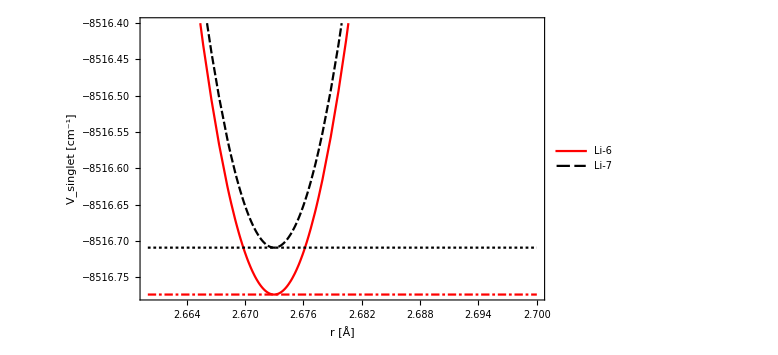

```mathematica
Plot[{Singlet6VMLR[r],SingletVMLR[r],-SingletDe,-Singlet6De},{r,2.660,2.70},PlotRange->{-8516.4,-8516.8},Frame->True,Frame->True,FrameLabel->{"r [Å]", "V_singlet [cm^-1]"},ImageSize->Large,PlotStyle->{Red,Black,Black,Red},PlotLegends->{"Li-6","Li-7"},LabelStyle->Large]
```

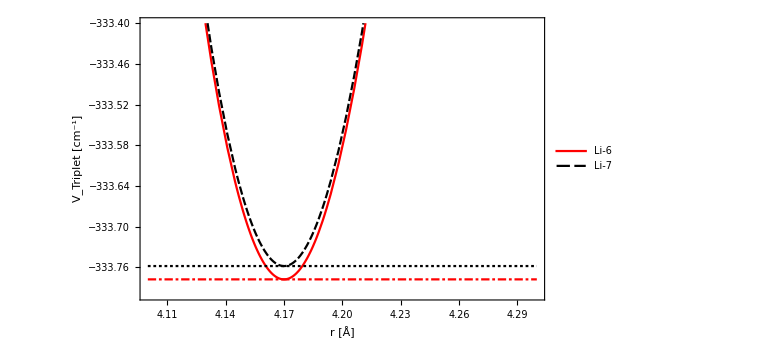

```mathematica
Plot[{Triplet6VMLR[r],TripletVMLR[r],-TripletDe,-Triplet6De},{r,4.1,4.3},PlotRange->{-333.8,-333.4},Frame->True,Frame->True,FrameLabel->{"r [Å]", "V_Triplet [cm^-1]"},ImageSize->Large,PlotStyle->{Red,Black,Black,Red},PlotLegends->{"Li-6","Li-7"},LabelStyle->Large]
```

```mathematica
Asymptotic[TripletVMLR[r],r->∞]
```

-(6.7185×10^6)/r^6

General::munfl: Exp[-56869.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-63610.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73499.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

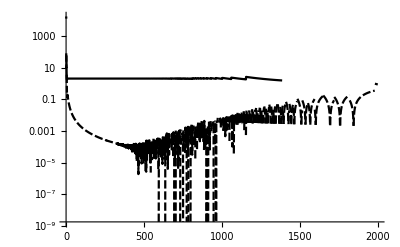

```mathematica
LogPlot[{Abs[(SingletVMLR[r]-Singletulr[r,SingletC6,SingletC8,SingletC10])/SingletVMLR[r]],Abs[(TripletVMLR[r]+(6.7185 10^6)/r^6)/TripletVMLR[r]]},{r,1,2000}]
```

#### Convert potentials to atomic units

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
```

```mathematica
XLi6dat = Import["/Users/alysonlaskowski/LiScattering/fort.10"];
ALi6dat = Import["/Users/alysonlaskowski/LiScattering/fort.30"];
XLi6 = Interpolation[XLi6dat];
ALi6=Interpolation[ALi6dat];
```

```mathematica
Rmax=400;
Rmin=0.005;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
XLi6MLRdat = Table[{RGrid[[i]],Singlet6VMLR[RGrid[[i]]]},{i,1,NR}];
XLi6MLRHBdat = Table[{RGrid[[i]]*AngstrominBohr, XLi6MLRdat[[i,2]]*invcminHartree},{i,1,Length[XLi6MLRdat]}];
```

```mathematica
XLi6MLRHB = Interpolation[XLi6MLRHBdat]
```

InterpolatingFunction[…]

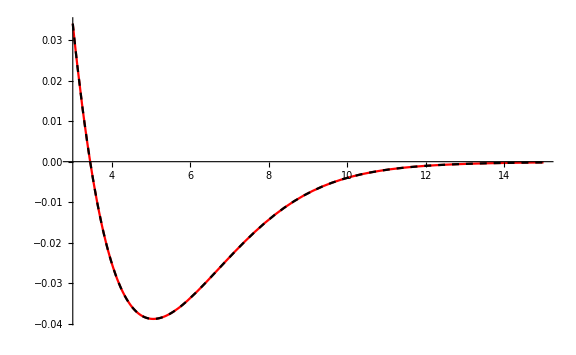

```mathematica
Plot[{XLi6MLRHB[r],XLi6[r]},{r,3.0,15},PlotStyle->{Red,Dashed},ImageSize->Large]
```

```mathematica
ALi6MLRdat = Table[{RGrid[[i]],Triplet6VMLR[RGrid[[i]]]},{i,1,NR}];
ALi6MLRHBdat = Table[{RGrid[[i]]*AngstrominBohr, ALi6MLRdat[[i,2]]*invcminHartree},{i,1,Length[ALi6MLRdat]}];
ALi6MLRHB = Interpolation[ALi6MLRHBdat]
```

General::munfl: Exp[-708.736] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.214] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.693] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

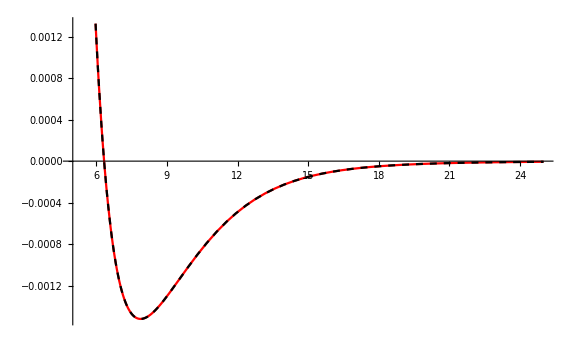

```mathematica
Plot[{ALi6MLRHB[r],ALi6[r]},{r,5.0,25},PlotStyle->{Red,Dashed},ImageSize->Large]
```

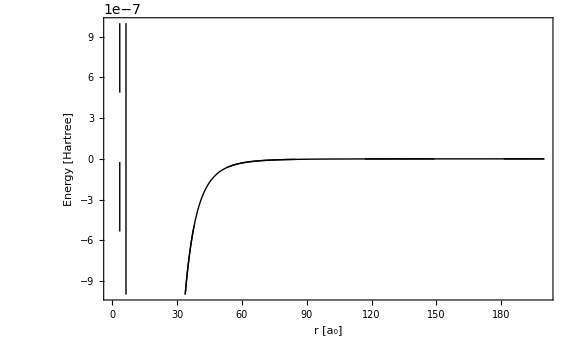

```mathematica
Plot[{ALi6MLRHB[r],XLi6MLRHB[r]},{r,3.0,200},Frame->True,ImageSize->Large,PlotStyle->{{Black,Thick},{Black,Thick,Dashing[2]},{Red,Dashed}},PlotRange->{-10^-6,10^-6},LabelStyle->Large,FrameLabel->{"r [a_0]","Energy [Hartree]"}]
```

```mathematica
Plot[{ALi6MLRHB[r],TripletHBMLR[r],XLi6MLRHB[r],SingletHBMLR[r]},{r,3.0,25},Frame->True,ImageSize->Large,PlotStyle->{{Black,Thick},{Red,Dashed},{Black,Thick,Dashing[2]},{Red,Dashed}},PlotRange->{-0.04,0.005},LabelStyle->Large,(*PlotLegends->Placed[{"Li_2","Li_2"},{Right,Center}],*)FrameLabel->{"r [a_0]","Energy [Hartree]"},Epilog->{Inset[psg,{18,-0.030},{Automatic,Automatic},{11,0.25}],Inset[ptp,{18,-0.010},{Automatic,Automatic},{11,0.25}]}]
```

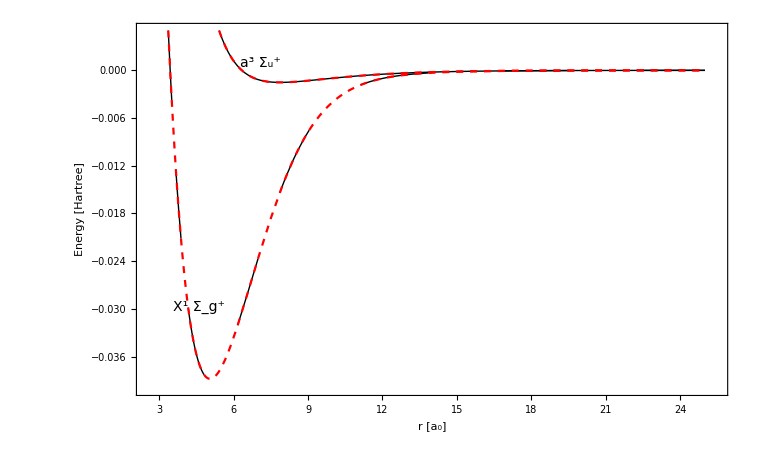

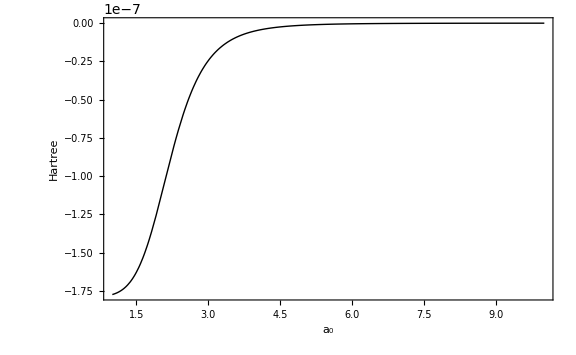

```mathematica
ptp=Plot[{(*ALi6MLRHB[r]-TripletHBMLR[r]*)TripletΔVad[r*AngstrominBohr]*invcminHartree},{r,1,10},Frame->True,ImageSize->Large,PlotStyle->{{Black,Thick},{Red,Dashed}},LabelStyle->Medium, FrameLabel->{"a_0","Hartree"},PlotRange->Full(*PlotRange->{-0.0015209,-0.0015198}*)]
```

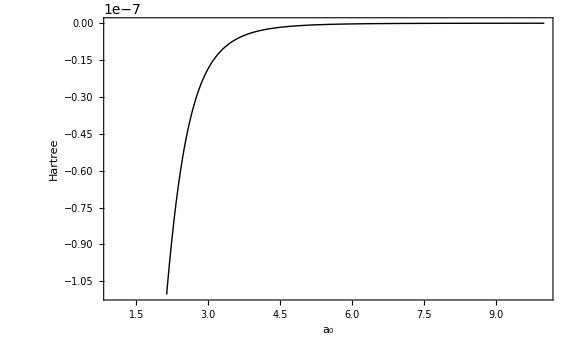

```mathematica
psg =Plot[{(*XLi6MLRHB[r]-SingletHBMLR[r]*)SingletΔVad[r*AngstrominBohr]*invcminHartree},{r,1,10},Frame->True,ImageSize->Large,PlotStyle->{{Black,Thick},{Red,Dashed}},(*PlotRange->{-0.0388055,-0.038801},*)LabelStyle->Medium, FrameLabel->{"a_0","Hartree"}]
```

### Bound State Calculation Using DVR

```mathematica
χGL[nodes_,i_,x_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,1,i-1}]Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,i+1,M+2}]
```

```mathematica
M=300;precision=20;{xnodes,weights,errwn}=NIntegrate`LobattoRuleData[M+2,precision];
```

```mathematica
a=2;b=50;xn=xnodes(b-a)+a; wn = weights(b-a);
```

```mathematica
χ=Table[wn[[i]]^(-1/2)χGL[xn,i,xn[[j]]],{i,1,M+2},{j,1,M+2}];
```

```mathematica
χp=Table[wn[[i]]^(-1/2)D[χGL[xn,i,x],x]/.x->xn[[j]],{i,1,M+2},{j,1,M+2}];
```

```mathematica
W=DiagonalMatrix[wn];
```

```mathematica
TLi6=1/massLi6 Table[χp[[i]].W.χp[[j]],{i,2,M+1},{j,2,M+1}];
VLi6Singlet=DiagonalMatrix[XLi6MLRHB[xn[[2;;M+1]]]];
```

```mathematica
VLi6Triplet=DiagonalMatrix[ALi6MLRHB[xn[[2;;M+1]]]];
```

```mathematica
Singlet6EigenSystem=Sort[Transpose[Eigensystem[TLi6+VLi6Singlet]]];
Vals6Singlet = Table[Singlet6EigenSystem[[i]][[1]],{i,1,Length[Singlet6EigenSystem]}];
Vals6Singlet[[1;;40]]
```

{-0.0379443,-0.0362427,-0.0345688,-0.032923,-0.0313055,-0.0297166,-0.0281568,-0.0266263,-0.0251257,-0.0236555,-0.0222162,-0.0208085,-0.0194332,-0.0180909,-0.0167825,-0.0155091,-0.0142716,-0.0130713,-0.0119095,-0.0107876,-0.00970718,-0.00866999,-0.00767798,-0.00673325,-0.00583813,-0.00499517,-0.00420717,-0.00347715,-0.00280842,-0.00220447,-0.00166899,-0.00120574,-0.000818295,-0.000509524,-0.000280587,-0.000128842,-0.000044491,-8.90913×10^-6,-1.40317×10^-8,3.09065×10^-6}

```mathematica
evalsdat[[1;;39]]
```

{{1,-0.0381764},{2,-0.0364044},{3,-0.0337842},{4,-0.0327585},{5,-0.0310362},{6,-0.0293249},{7,-0.0270598},{8,-0.0248295},{9,-0.0241875},{10,-0.022909},{11,-0.0223307},{12,-0.0213831},{13,-0.0203382},{14,-0.0188043},{15,-0.0175447},{16,-0.0162658},{17,-0.0144748},{18,-0.0135809},{19,-0.0126972},{20,-0.0116627},{21,-0.0107649},{22,-0.00915303},{23,-0.00803375},{24,-0.00711591},{25,-0.00644296},{26,-0.00543799},{27,-0.00463985},{28,-0.00361946},{29,-0.0032368},{30,-0.00246339},{31,-0.00186177},{32,-0.00149931},{33,-0.00101076},{34,-0.000668098},{35,-0.000337571},{36,-0.000161587},{37,-0.000063121},{38,-0.0000146795},{39,-9.36792×10^-7}}

```mathematica
Triplet6EigenSystem=Sort[Transpose[Eigensystem[TLi6+VLi6Triplet]]];
```

```mathematica
Vals6Triplet = Table[Triplet6EigenSystem[[i]][[1]],{i,1,Length[Triplet6EigenSystem]}];
```

```mathematica
Vals6Triplet[[1;;11]]
```

{-0.00136406,-0.00107832,-0.00082718,-0.000609681,-0.000425482,-0.000274701,-0.000157729,-0.00007482,-0.0000250167,-3.72354×10^-6,9.151×10^-7}

```mathematica
TLi7=1/massLi7 Table[χp[[i]].W.χp[[j]],{i,2,M+1},{j,2,M+1}];
VLi7Singlet=DiagonalMatrix[SingletHBMLR[xn[[2;;M+1]]]];
VLi7Triplet=DiagonalMatrix[TripletHBMLR[xn[[2;;M+1]]]];
```

```mathematica
Singlet7EigenSystem=Sort[Transpose[Eigensystem[TLi7+VLi7Singlet]]];
Vals7Singlet = Table[Singlet7EigenSystem[[i]][[1]],{i,1,Length[Singlet7EigenSystem]}];
Vals7Singlet[[1;;43]]
```

{-0.0380075,-0.03643,-0.0348763,-0.0333466,-0.0318411,-0.0303601,-0.0289038,-0.0274725,-0.0260666,-0.0246865,-0.0233325,-0.0220052,-0.0207051,-0.0194327,-0.0181887,-0.0169737,-0.0157885,-0.014634,-0.013511,-0.0124206,-0.0113638,-0.0103419,-0.00935612,-0.00840795,-0.00749899,-0.00663097,-0.0058056,-0.00502485,-0.00429127,-0.00360775,-0.00297655,-0.00239933,-0.00187849,-0.00141778,-0.00102133,-0.000692244,-0.000431955,-0.00023991,-0.000112464,-0.0000405792,-8.97973×10^-6,-2.90082×10^-7,2.41313×10^-6}

```mathematica
Triplet7EigenSystem=Sort[Transpose[Eigensystem[TLi7+VLi7Triplet]]];
Vals7Triplet = Table[Triplet7EigenSystem[[i]][[1]],{i,1,Length[Triplet7EigenSystem]}];
Vals7Triplet[[1;;12]]
```

{-0.0013753,-0.00110831,-0.000871097,-0.000662833,-0.000483148,-0.000332043,-0.000209777,-0.000116669,-0.0000526425,-0.0000161032,-1.89333×10^-6,1.24614×10^-6}

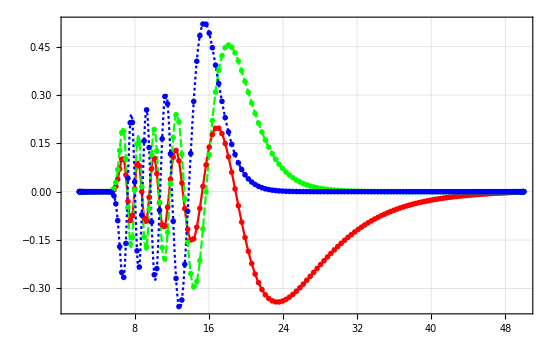

```mathematica
ListPlot[Table[Transpose[{xn,Triplet6EigenSystem[[ii]][[2]].χ[[2;;M+1]]}],{ii,10,8,-1}],Joined->True,InterpolationOrder->3,Frame->True,GridLines->Automatic,PlotRange->Full,PlotStyle->{Red,Green,Blue}]
```

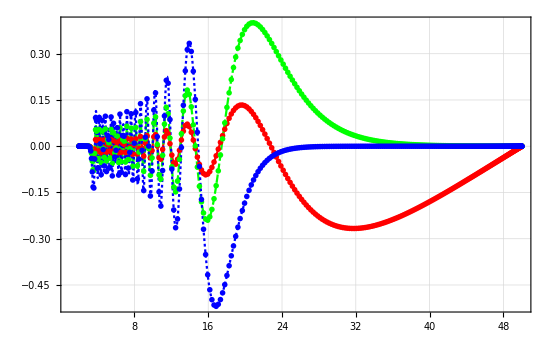

```mathematica
ListPlot[Table[Transpose[{xn,Singlet6EigenSystem[[ii]][[2]].χ[[2;;M+1]]}],{ii,39,37,-1}],Joined->True,InterpolationOrder->3,Frame->True,GridLines->Automatic,PlotRange->Full,PlotStyle->{Red,Green,Blue}]
```

### Zeeman and Hyperfine Interactions and Projection Operators

#### Define parameters in atomic units and define basis with M_F=0

```mathematica
Li6c6H = (SingletC6*invcminHartree*AngstrominBohr^6)
Li6c8H = (SingletC8*invcminHartree*AngstrominBohr^8)
Li6c10H= (SingletC10*invcminHartree*AngstrominBohr^10)
```

1393.39

83425.5

7.37211×10^6

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;

Li7ATHz = 401.75204335 * 10^-6;
Li6ATHz = 152.0*10^-6;
Li7Ainvcm = (Li7ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Li6Ainvcm = (Li6ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Li7AH = Li7Ainvcm*invcminHartree
Li6AH = Li6Ainvcm*invcminHartree
```

6.10725×10^-8

2.31064×10^-8

```mathematica
μbTHz = (9.27*10^-24)/(6.626*10^-34)*10^-12*(1/10^4);
μnTHz = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4);
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μninvcm = (μnTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree
μnH=μninvcm*invcminHartree
```

2.12675×10^-10

1.15876×10^-13

```mathematica
MF0basis = {{1/2,1/2,1/2,-1/2},{1/2,1/2,3/2,-1/2},{1/2,-1/2,3/2,1/2},{3/2,-3/2,3/2,3/2},{3/2,1/2,3/2,-1/2}};
```

#### Projection Operators

```mathematica
Singlet6Proj = {{1/3,0,0,-1/3,-1/3},{0,1/3,1/3,-1/(3 √2),1/(3 √2)},{0,1/3,1/3,-1/(3 √2),1/(3 √2)},{-1/3,-1/(3 √2),-1/(3 √2),1/2,1/6},{-1/3,1/(3 √2),1/(3 √2),1/6,1/2}};
Triplet6Proj={{2/3,0,0,1/3,1/3},{0,2/3,-1/3,1/(3 √2),-1/(3 √2)},{0,-1/3,2/3,1/(3 √2),-1/(3 √2)},{1/3,1/(3 √2),1/(3 √2),1/2,-1/6},{1/3,-1/(3 √2),-1/(3 √2),-1/6,1/2}};
```

```mathematica
MatrixForm[Singlet6Proj+Triplet6Proj]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

#### Hyperfine and Zeeman Interaction

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_,μn_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μn B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
Li6HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[MF0basis[[j,1]],MF0basis[[j,3]]] KroneckerDelta[MF0basis[[j,2]],MF0basis[[j,4]]])(1+KroneckerDelta[MF0basis[[jp,1]],MF0basis[[jp,3]]] KroneckerDelta[MF0basis[[jp,2]],MF0basis[[jp,4]]]))))*(HZ[MF0basis[[j,1]],MF0basis[[j,2]],MF0basis[[jp,1]],MF0basis[[jp,2]],Li6s,Li6i,Li6gs,Li6gi,Li6AH,B,μbH,μnH]KroneckerDelta[MF0basis[[j,3]],MF0basis[[jp,3]]]KroneckerDelta[MF0basis[[j,4]],MF0basis[[jp,4]]]+HZ[MF0basis[[j,3]],MF0basis[[j,4]],MF0basis[[jp,3]],MF0basis[[jp,4]],Li6s,Li6i,Li6gs,Li6gi,Li6AH,B,μbH,μnH]KroneckerDelta[MF0basis[[j,1]],MF0basis[[jp,1]]]KroneckerDelta[MF0basis[[j,2]],MF0basis[[jp,2]]]+(-1)^p(-1)^l HZ[MF0basis[[j,3]],MF0basis[[j,4]],MF0basis[[jp,1]],MF0basis[[jp,2]],Li6s,Li6i,Li6gs,Li6gi,Li6AH,B,μbH,μnH]KroneckerDelta[MF0basis[[j,1]],MF0basis[[jp,3]]]KroneckerDelta[MF0basis[[j,2]],MF0basis[[jp,4]]]+(-1)^p(-1)^l HZ[MF0basis[[j,1]],MF0basis[[j,2]],MF0basis[[jp,3]],MF0basis[[jp,4]],Li6s,Li6i,Li6gs,Li6gi,Li6AH,B,μbH,μnH]KroneckerDelta[MF0basis[[j,3]],MF0basis[[jp,1]]]KroneckerDelta[MF0basis[[j,4]],MF0basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi6[B_]=FullSimplify[Li6HZsym[1,0,B]];
HLi6total[r_,B_]= HZsymLi6[B]+Triplet6Proj*ALi6MLRHB[r]+Singlet6Proj*XLi6MLRHB[r];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1,-1},{1/2,-1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1,0},{1/2,-1/2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
HZ1 = -4.62127*10^-8;
```

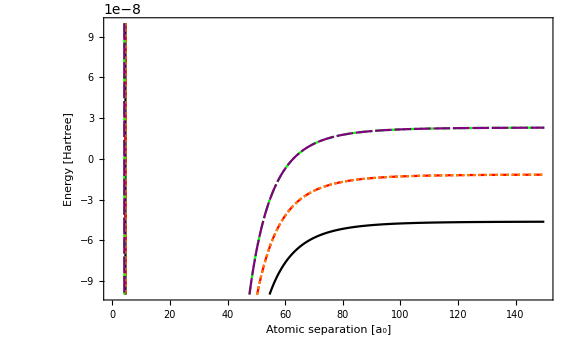

```mathematica
phf =Plot[{HLi6total[r,0][[1,1]],HLi6total[r,0][[2,2]],HLi6total[r,0][[3,3]],HLi6total[r,0][[4,4]],HLi6total[r,0][[5,5]]} ,{r,1.0,150},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotRange->{-1*10^-7,1*10^-7},PlotStyle->{Black,Red,Orange,Green,Purple}]
```

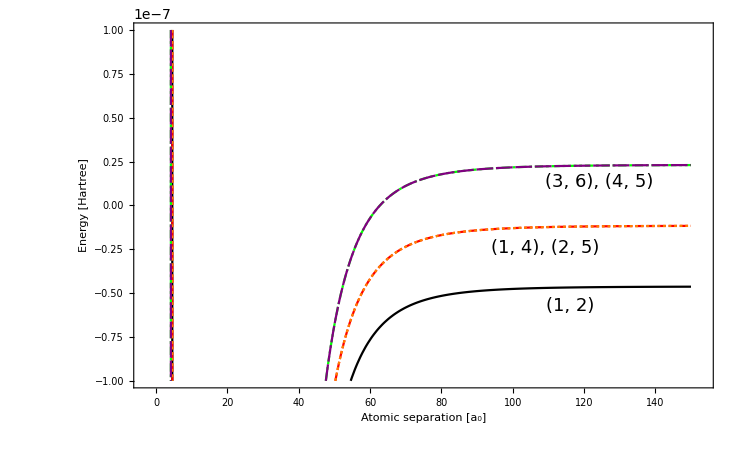

```mathematica
Clear[EigenTable]
```

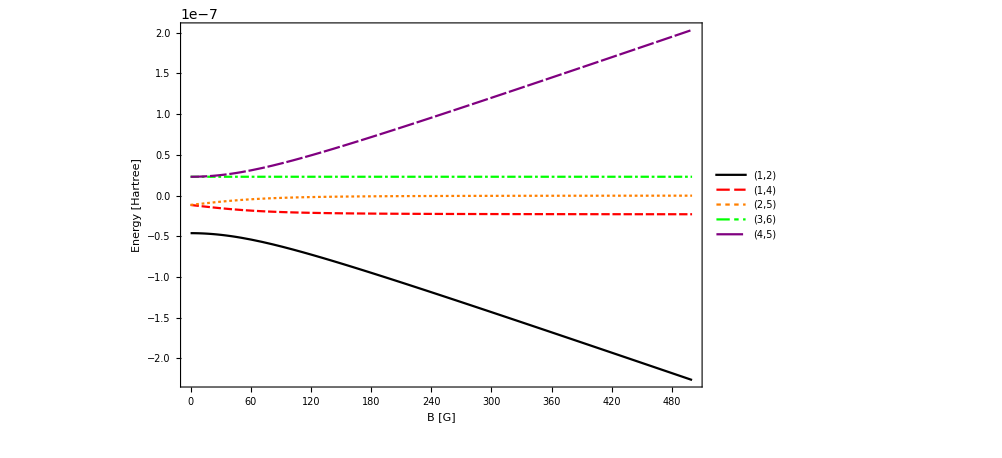

```mathematica
EigenTable[B_]:= Sort[Eigenvalues[HZsymLi6[B]]];
phz =Plot[{EigenTable[B][[1]],EigenTable[B][[2]],EigenTable[B][[3]],EigenTable[B][[4]],EigenTable[B][[5]]},{B,0,500},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large,PlotLegends->Placed[LineLegend[{Style["(1,2)",16],Style["(1,4)",16],Style["(2,5)",16],Style["(3,6)",16],Style["(4,5)",16]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{Right,Center}],PlotStyle->{Black,Red,Orange,Green,Purple}]
```

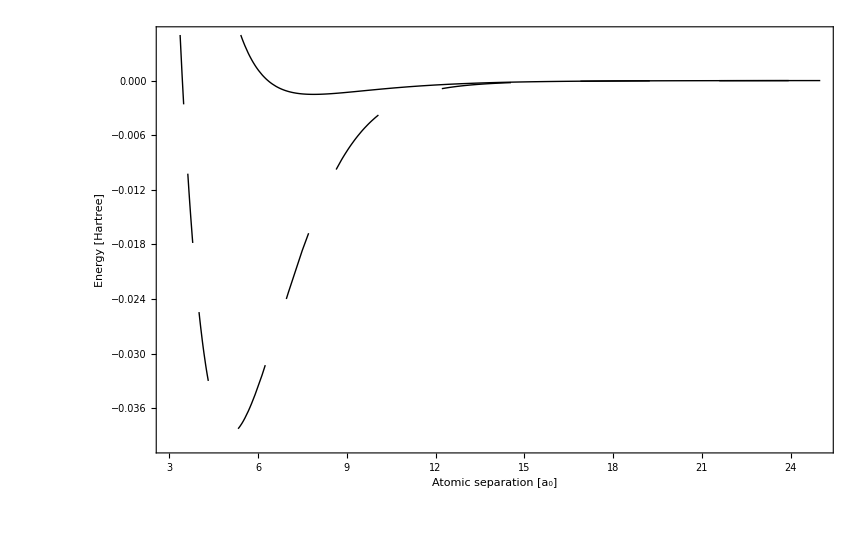

```mathematica
Plot[{ALi6MLRHB[r],XLi6MLRHB[r]},{r,3.0,25},Frame->True,ImageSize->Large,PlotStyle->{{Black,Thick},{Black,Thick,Dashing[2]},{Red,Dashed}},PlotRange->{-0.04,0.0050},LabelStyle->Large,(*PlotLegends->Placed[{"Li_2","Li_2"},{Right,Center}],*)FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},Epilog->{Inset[phf,{17,-0.020},{Automatic,Automatic},{16,0.25}]}]
```

```mathematica
1/HartreeinLi6vdw
```

2.3153×10^-8

### Calculate the Scattering Lengths for X and A states of ^6 Li_2

```mathematica
μLi6 = massLi6/2
Triplet[a_,r_]:= ALi6MLRHB[r]+If[r<Tripletre*AngstrominBohr, a(r-Tripletre*AngstrominBohr)^2,0];
Singlet[a_,r_]:= XLi6MLRHB[r]+If[r<Singletre*AngstrominBohr, a(r-Singletre*AngstrominBohr)^2,0];
```

5482.45

```mathematica
CalcCotanDeltaTriplet[Εtest_,rmax_,rmin_,μ_,a_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+Triplet[a,r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERETriplet[rmax_,rmin_,ΕMin_,ΕMax_,μ_,a_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaTriplet[Εtest,rmax,rmin,μ,a]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
{Tripletascat,Tripletreff,TripletEREData}=CalcERETriplet[500,2,10^-10,5*10^-9,μLi6,1.5432*10^-6]
```

{-2160.,91.7619,{{1.09649×10^-6,0.000520793},{6.4693×10^-6,0.000762988},{0.0000118421,0.00100599},{0.0000172149,0.00124989},{0.0000225877,0.00149473},{0.0000279605,0.00174058},{0.0000333333,0.00198749},{0.0000387061,0.00223549},{0.0000440789,0.00248463},{0.0000494517,0.00273494},{0.0000548245,0.00298646}}}

```mathematica
a = 1.5432*10^-6;
ALi6MLRNew[r_]:=Triplet[a,r]
```

```mathematica
CalcCotanDeltaSinglet[Εtest_,rmax_,rmin_,μ_,a_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+Singlet[a,r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERE[rmax_,rmin_,ΕMin_,ΕMax_,μ_,a_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaSinglet[Εtest,rmax,rmin,μ,a]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
{Singletascat,Singletreff,SingletEREData}=CalcERE[500,2,10^-10,0.5*10^-8,μLi6,1.337*10^-6]
```

{45.1446,36.7645,{{1.09649×10^-6,-0.0221409},{6.4693×10^-6,-0.0220355},{0.0000118421,-0.0219321},{0.0000172149,-0.0218303},{0.0000225877,-0.02173},{0.0000279605,-0.0216311},{0.0000333333,-0.0215333},{0.0000387061,-0.0214366},{0.0000440789,-0.0213408},{0.0000494517,-0.0212458},{0.0000548245,-0.0211515}}}

```mathematica
b =(* 1.337*10^-5*)1.337*10^-6;
XLi6MLRNew[r_]:=Singlet[b,r]
```

#### Triplet and Singlet Wavefunctions

-Graphics-

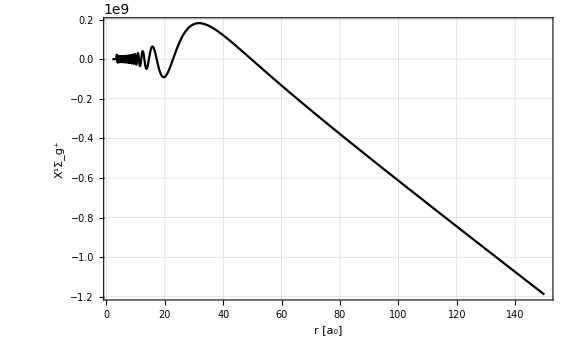

```mathematica
Etest = 10^-16;
soltp = NDSolveValue[{-1/(2 μLi6)u''[r]+ ALi6MLRNew[r]*u[r]==Etest u[r],u[2.0]==0,u'[2.0]==10^-10},u,{r,2.0,500}];
solsg = NDSolveValue[{-1/(2 μLi6)u''[r]+ XLi6MLRNew[r]*u[r]==Etest u[r],u[2.0]==0,u'[2.0]==10^-10},u,{r,2.0,500}];
Plot[{soltp[r]},{r,2.0,150},Frame->True,ImageSize->Large,GridLines->Automatic,FrameLabel->{"r [a_0]","a^3Σ_u^+"}]
Plot[{solsg[r]},{r,2.0,150},Frame->True,ImageSize->Large,GridLines->Automatic,FrameLabel->{"r [a_0]","X^1Σ_g^+"}]
```

### Singlet and Triplet Bound States

```mathematica
μLi6
XLi6De=Singlet6De*invcminHartree
ALi6De=Triplet6De*invcminHartree
```

5482.45

0.0388053

0.0015208

```mathematica
ℒt=-1/(2 μLi6)u''[x]+(ALi6MLRNew[x]+ALi6De)*u[x];
{valsTriplet,funsTriplet}=NDEigensystem[ℒt,u[x],{x,2.0,200},20, Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsTriplet-ALi6De
```

{-0.00136395,-0.00107811,-0.000826926,-0.000609426,-0.000425247,-0.000274499,-0.000157572,-0.0000747127,-0.00002496,-3.70716×10^-6,3.35414×10^-8,3.01764×10^-7,6.96659×10^-7,1.26604×10^-6,2.00795×10^-6,2.75614×10^-6,3.91498×10^-6,5.18332×10^-6,6.88461×10^-6,7.83693×10^-6}

```mathematica
valsTriplet[[1;;10]]-ALi6De
```

{-0.00136395,-0.00107811,-0.000826926,-0.000609426,-0.000425247,-0.000274499,-0.000157572,-0.0000747127,-0.00002496,-3.70716×10^-6}

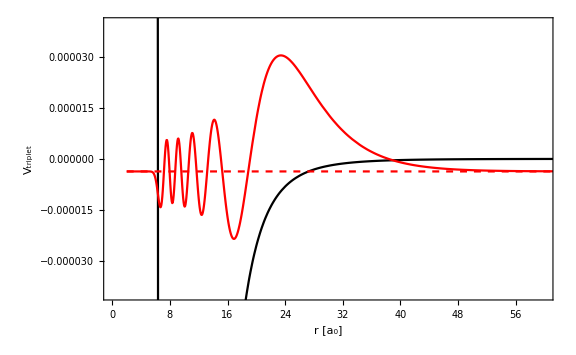

```mathematica
pvt=Plot[ALi6MLRNew[x],{x,2.0,200},PlotRange->{-ALi6De,0.001}];
p1=Plot[(Evaluate[.0001funsTriplet[[10;;10]]+valsTriplet[[10;;10]]-ALi6De]),{x,2.0,200},PlotRange->All,PlotStyle->Red];
Show[{pvt,p1,Plot[valsTriplet[[10]]-ALi6De,{x,2.0,200},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{0,60},{-0.00004,0.00004}},FrameLabel->{"r [a_0]","V_triplet"},ImageSize->Large]
```

```mathematica
ℒs=-1/(2 μLi6)u''[x]+(XLi6MLRHB[x]+XLi6De)*u[x];
{valsSinglet,funsSinglet}=NDEigensystem[ℒs,u[x],{x,2.0,200},45,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix «1» in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsSinglet-XLi6De
```

{-0.0379443,-0.0362427,-0.0345688,-0.032923,-0.0313055,-0.0297166,-0.0281568,-0.0266263,-0.0251257,-0.0236555,-0.0222162,-0.0208085,-0.0194332,-0.0180909,-0.0167825,-0.0155091,-0.0142716,-0.0130713,-0.0119095,-0.0107876,-0.00970718,-0.00866999,-0.00767798,-0.00673325,-0.00583813,-0.00499517,-0.00420717,-0.00347715,-0.00280841,-0.00220446,-0.00166899,-0.00120576,-0.000818325,-0.000509551,-0.000280605,-0.000128851,-0.0000444944,-8.67052×10^-6,5.26399×10^-6,0.0000240045,0.0000566268,0.0000804237,0.000121729,0.000163274,0.000221586}

```mathematica
valsSinglet[[1;;38]]-XLi6De
```

{-0.0379443,-0.0362427,-0.0345688,-0.032923,-0.0313055,-0.0297166,-0.0281568,-0.0266263,-0.0251257,-0.0236555,-0.0222162,-0.0208085,-0.0194332,-0.0180909,-0.0167825,-0.0155091,-0.0142716,-0.0130713,-0.0119095,-0.0107876,-0.00970718,-0.00866999,-0.00767798,-0.00673325,-0.00583813,-0.00499517,-0.00420717,-0.00347715,-0.00280841,-0.00220446,-0.00166899,-0.00120576,-0.000818325,-0.000509551,-0.000280605,-0.000128851,-0.0000444944,-8.67052×10^-6}

```mathematica
evalsdat =Import["/Users/alysonlaskowski/1D-Schrodinger-bsplines-BOUND-STATES/evals.dat"];
```

```mathematica
evalsdat[[1;;39]]
```

{{1,-0.0381764},{2,-0.0364044},{3,-0.0337842},{4,-0.0327585},{5,-0.0310362},{6,-0.0293249},{7,-0.0270598},{8,-0.0248295},{9,-0.0241875},{10,-0.022909},{11,-0.0223307},{12,-0.0213831},{13,-0.0203382},{14,-0.0188043},{15,-0.0175447},{16,-0.0162658},{17,-0.0144748},{18,-0.0135809},{19,-0.0126972},{20,-0.0116627},{21,-0.0107649},{22,-0.00915303},{23,-0.00803375},{24,-0.00711591},{25,-0.00644296},{26,-0.00543799},{27,-0.00463985},{28,-0.00361946},{29,-0.0032368},{30,-0.00246339},{31,-0.00186177},{32,-0.00149931},{33,-0.00101076},{34,-0.000668098},{35,-0.000337571},{36,-0.000161587},{37,-0.000063121},{38,-0.0000146795},{39,-9.36792×10^-7}}

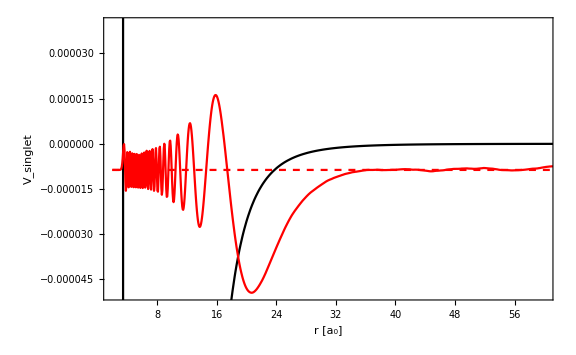

```mathematica
pvs=Plot[XLi6MLRHB[x],{x,2.0,200},PlotRange->{-XLi6De,0.001}];
p2=Plot[(Evaluate[.0001funsSinglet[[38;;38]]+valsSinglet[[38;;38]]-XLi6De]),{x,2.0,200},PlotRange->All,PlotStyle->Red];
Show[{pvs,p2,Plot[valsSinglet[[38]]-XLi6De,{x,2.0,200},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{2,60},{-0.00005,0.00004}},FrameLabel->{"r [a_0]","V_singlet"},ImageSize->Large]
```

### Convert to van der Waals Units

```mathematica
βLi6 = β/.Solve[(-SingletC6*AngstrominBohr^6*invcminHartree)/β^6-(SingletC8*AngstrominBohr^8*invcminHartree)/β^8-(SingletC10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μLi6 β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

62.7616

```mathematica
BohrinLi6vdw = 1/62.7616
Li6vdwinHartree = 1/(2 μLi6 βLi6^2)
HartreeinLi6vdw = 1/Li6vdwinHartree
```

0.0159333

2.3153×10^-8

4.31909×10^7

```mathematica
Li6c6vdw = (2 μLi6)/βLi6^4(SingletC6*invcminHartree*AngstrominBohr^6)
Li6c8vdw = (2 μLi6)/βLi6^6(SingletC8*invcminHartree*AngstrominBohr^8)
Li6c10vdw = (2 μLi6)/βLi6^8(SingletC10*invcminHartree*AngstrominBohr^10)
```

0.984697

0.0149672

0.000335774

```mathematica
μbvdw = μbH*HartreeinLi6vdw;
μnvdw = μnH*HartreeinLi6vdw;
```

```mathematica
Rmax=750;
Rmin=0.085;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];

ALi6MLRdatNew = Table[{RGrid[[i]],ALi6MLRNew[RGrid[[i]]]},{i,1,NR}];
ALi6MLRVDWdatNew = Table[{RGrid[[i]]*BohrinLi6vdw, ALi6MLRdatNew[[i,2]]*HartreeinLi6vdw},{i,1,Length[ALi6MLRdat]}];
ALi6VDW= Interpolation[ALi6MLRVDWdatNew]
```

InterpolatingFunction[…]

```mathematica
XLi6MLRdat =Table[{RGrid[[i]],XLi6MLRHB[RGrid[[i]]]},{i,1,NR}];
XLi6VDWdat = Table[{XLi6MLRdat[[i,1]]*BohrinLi6vdw,XLi6MLRdat[[i,2]]*HartreeinLi6vdw},{i,1,Length[ALi6MLRHBdat]}];
XLi6VDW = Interpolation[XLi6VDWdat]
```

InterpolatingFunction[…]

```mathematica
XLi6MLRdatNew =Table[{RGrid[[i]],XLi6MLRNew[RGrid[[i]]]},{i,1,NR}];
XLi6VDWdatNew = Table[{RGrid[[i]]*BohrinLi6vdw,XLi6MLRdatNew[[i,2]]*HartreeinLi6vdw},{i,1,Length[ALi6MLRHBdat]}];
XLi6VDWNew = Interpolation[XLi6VDWdatNew]
```

InterpolatingFunction[…]

```mathematica
Li6vlr[r_]:= -Li6c6vdw/r^6-Li6c8vdw/r^8-Li6c10vdw/r^10;
Li6vlrC6[r_]:= -1/r^6;
```

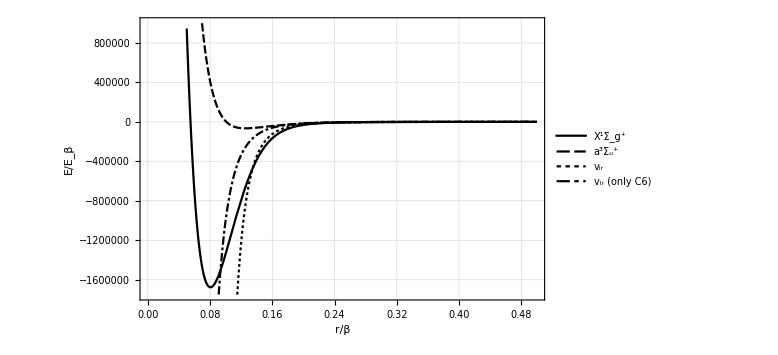

```mathematica
Plot[{XLi6VDWNew[r],ALi6VDW[r],Li6vlr[r],Li6vlrC6[r]},{r,0.05,0.50},PlotRange->{-1.75*10^6,10^6},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+","v_lr","v_lr (only C6)"}]
```

### MQDT Calculation

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=(*Sqrt[k/π]*) r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= (*Sqrt[k/π] *)r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r;
```

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
rx = 10.0*BohrinLi6vdw;
rf = 300*BohrinLi6vdw;
r0 = 40*BohrinLi6vdw;
rmin = 2.0*BohrinLi6vdw;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - Li6vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Li6vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Li6vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕLi6=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
CalcQuantumDefect6[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
g0=-α[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0=α[r0]Sin[ϕ+phaseint];
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
μTLi6 = CalcQuantumDefect6[0,0,rmin*.9,rmax,r0,rx,rf,r,nr,ALi6VDW,ϕLi6[[1]]]
```

0.495494

```mathematica
μSLi6 = CalcQuantumDefect6[0,0,rmin,rmax,r0,rx,rf,r,nr,XLi6VDWNew,ϕLi6[[1]]]
```

-0.149231

```mathematica
μTLi6Table=Table[{Etest, CalcQuantumDefect6[Etest,0,rmin,r0,r0,rx,rf,r,nr,ALi6VDW,ϕLi6[[1]]]},{Etest,-50,100,1}];
μSLi6Table=Table[{Etest, CalcQuantumDefect6[Etest,0,rmin,r0,r0,rx,rf,r,nr,XLi6VDW,ϕLi6[[1]]]},{Etest,-50,100,1}];
```

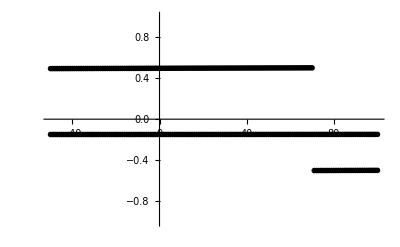

```mathematica
ListPlot[{μSLi6Table,μTLi6Table},PlotRange->{-1.0,1.0}]
```

```mathematica
Li6Avdw=Li6AH*HartreeinLi6vdw;
Li6HZsymVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[MF0basis[[j,1]],MF0basis[[j,3]]] KroneckerDelta[MF0basis[[j,2]],MF0basis[[j,4]]])(1+KroneckerDelta[MF0basis[[jp,1]],MF0basis[[jp,3]]] KroneckerDelta[MF0basis[[jp,2]],MF0basis[[jp,4]]]))))*(HZ[MF0basis[[j,1]],MF0basis[[j,2]],MF0basis[[jp,1]],MF0basis[[jp,2]],Li6s,Li6i,Li6gs,Li6gi,Li6Avdw,B,μbvdw,μnvdw]KroneckerDelta[MF0basis[[j,3]],MF0basis[[jp,3]]]KroneckerDelta[MF0basis[[j,4]],MF0basis[[jp,4]]]+HZ[MF0basis[[j,3]],MF0basis[[j,4]],MF0basis[[jp,3]],MF0basis[[jp,4]],Li6s,Li6i,Li6gs,Li6gi,Li6Avdw,B,μbvdw,μnvdw]KroneckerDelta[MF0basis[[j,1]],MF0basis[[jp,1]]]KroneckerDelta[MF0basis[[j,2]],MF0basis[[jp,2]]]+(-1)^p(-1)^l HZ[MF0basis[[j,3]],MF0basis[[j,4]],MF0basis[[jp,1]],MF0basis[[jp,2]],Li6s,Li6i,Li6gs,Li6gi,Li6Avdw,B,μbvdw,μnvdw]KroneckerDelta[MF0basis[[j,1]],MF0basis[[jp,3]]]KroneckerDelta[MF0basis[[j,2]],MF0basis[[jp,4]]]+(-1)^p(-1)^l HZ[MF0basis[[j,1]],MF0basis[[j,2]],MF0basis[[jp,3]],MF0basis[[jp,4]],Li6s,Li6i,Li6gs,Li6gi,Li6Avdw,B,μbvdw,μnvdw]KroneckerDelta[MF0basis[[j,3]],MF0basis[[jp,1]]]KroneckerDelta[MF0basis[[j,4]],MF0basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
Li6HZVDW[B_]=FullSimplify[Li6HZsymVDW[1,0,B]];
Li6HVDW[r_,B_]= Li6HZVDW[B]+Triplet6Proj*ALi6VDW[r]+Singlet6Proj*XLi6VDWNew[r];
Li6HZEigensystem[B_]:= Sort[Transpose[Eigensystem[Li6HZVDW[B]]]]
```

```mathematica
DD[B_]:= Transpose[{Li6HZEigensystem[B][[1]][[2]],Li6HZEigensystem[B][[2]][[2]],Li6HZEigensystem[B][[3]][[2]],Li6HZEigensystem[B][[4]][[2]],Li6HZEigensystem[B][[5]][[2]]}];
Li6Eth[B_]:= Table[Li6HZEigensystem[B][[j]][[1]],{j,1,5}];
```

```mathematica
Li6Eth[0]
```

{-1.99597,-0.498992,-0.498992,0.997984,0.997984}

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].Singlet6Proj.DD[B]*Tan[π μSLi6] + Transpose[DD[B]].Triplet6Proj.DD[B]*Tan[π μTLi6]
MatrixForm[KsrFTEI[100]]
```

(61.1549 | 10.1174 | -14.0896 | 13.5348 | 10.0133
10.1174 | 41.9759 | -10.0133 | -31.4769 | -4.89201
-14.0896 | -10.0133 | 14.5203 | -3.77168 | 23.0252
13.5348 | -31.4769 | -3.77168 | 35.0625 | -8.77155
10.0133 | -4.89201 | 23.0252 | -8.77155 | 58.1678)

```mathematica
KsrFTEIPP[B_]:= KsrFTEI[B][[1,1]];
KsrFTEIQP[B_]:=KsrFTEI[B][[2;;5,1]];
KsrFTEIPQ[B_]:=KsrFTEI[B][[1,2;;5]];
KsrFTEIQQ[B_]:=KsrFTEI[B][[2;;5,2;;5]];
```

```mathematica
En=500;
Emin = 10^-16;
Emax =100;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
```

```mathematica
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],ϕLi6[[1]]]]},{ii,1,Length[EGrid]}];
```

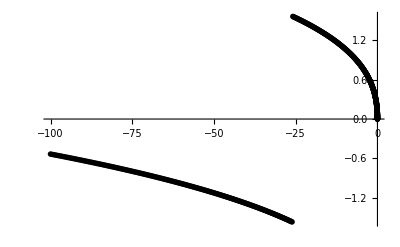

```mathematica
ListPlot[gammaTable,PlotRange->Full]
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]
]
```

319

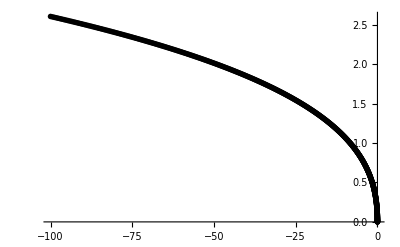

```mathematica
ListPlot[GammaTablenew]
```

```mathematica
GammaZero[ϵ_]:= abar√(-ϵ);
```

```mathematica
Fit[Table[{GammaTablenew[[ii,1]]*-1,GammaTablenew[[ii,2]]},{ii,1,Length[GammaTablenew]}],{ϵ^(1/2),ϵ,ϵ^(3/2),ϵ^2},ϵ]
```

0.44077 √ϵ-0.042385 ϵ+0.0039415 ϵ^(3/2)-0.000151251 ϵ^2

```mathematica
Gammanewfun[ϵ_]:=0.4407704946837574 √-ϵ+0.04238496088508142 ϵ+0.003941502623851877 (-ϵ)^(3/2)-0.00015125095088108382 ϵ^2;
```

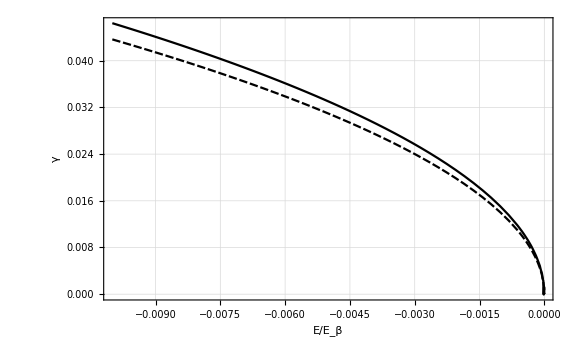

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
Plot[{Gammafun[ϵ],(*GammaZero[ϵ],*)Gammanewfun[ϵ]},{ϵ,-0.01,0},Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","γ"},LabelStyle->Large,ImageSize->Large]
```

```mathematica
CotGamma2[B_,Ε_]:= Cot[Gammafun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[2]])]];
CotGamma3[B_,Ε_]:= Cot[Gammafun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[3]])]];
CotGamma4[B_,Ε_]:= Cot[Gammafun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[4]])]];
CotGamma5[B_,Ε_]:= Cot[Gammafun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[5]])]];
CotGammaMatrix[B_,Ε_]:=DiagonalMatrix[{CotGamma2[B,Ε],CotGamma3[B,Ε],CotGamma4[B,Ε],CotGamma5[B,Ε]}];
```

```mathematica
CotGamma2New[B_,Ε_]:= Cot[Gammanewfun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[2]])]];
CotGamma3New[B_,Ε_]:= Cot[Gammanewfun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[3]])]];
CotGamma4New[B_,Ε_]:= Cot[Gammanewfun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[4]])]];
CotGamma5New[B_,Ε_]:= Cot[Gammanewfun[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[5]])]];
CotGammaMatrixNew[B_,Ε_]:=DiagonalMatrix[{CotGamma2New[B,Ε],CotGamma3New[B,Ε],CotGamma4New[B,Ε],CotGamma5New[B,Ε]}];
```

```mathematica
CotGamma2Zero[B_,Ε_]:= Cot[GammaZero[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[2]])]];
CotGamma3Zero[B_,Ε_]:= Cot[GammaZero[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[3]])]];
CotGamma4Zero[B_,Ε_]:= Cot[GammaZero[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[4]])]];
CotGamma5Zero[B_,Ε_]:= Cot[GammaZero[((Li6Eth[B][[1]]+Ε)-Li6Eth[B][[5]])]];
CotGammaMatrixZero[B_,Ε_]:=DiagonalMatrix[{CotGamma2Zero[B,Ε],CotGamma3Zero[B,Ε],CotGamma4Zero[B,Ε],CotGamma5Zero[B,Ε]}];
```

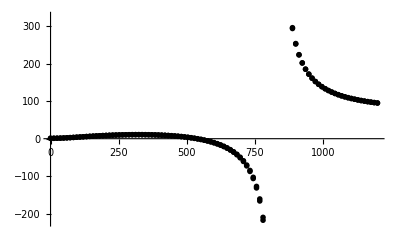

```mathematica
bmax = 1200;
bmin = 0;
bn = 100;
bgrid = Table[(bmax-bmin)/bn i,{i,0,bn}];
Etest = 10^-3;
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
KtildeFTEINew[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrixNew[B,Ε]].KsrFTEIQP[B];
(*KtildeFTEIZero[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrixZero[B,Ε]].KsrFTEIQP[B];*)
ListPlot[{Table[{bgrid[[ii]],KtildeFTEI[bgrid[[ii]],Etest]},{ii,1,bn+1}],Table[{bgrid[[ii]],KtildeFTEINew[bgrid[[ii]],Etest]},{ii,1,bn+1}](*,Table[{bgrid[[ii]],KtildeFTEIZero[bgrid[[ii]],Etest]},{ii,1,bn+1}]*)}]
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
```

```mathematica
EtaTable=Table[{EGrid[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]]},{ii,1,Length[EGrid]}];
```

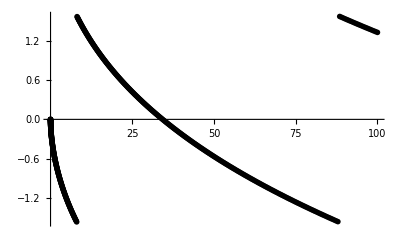

```mathematica
ListPlot[EtaTable]
```

```mathematica
EtaTablenew2=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]-π,EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]]
]
```

216

479

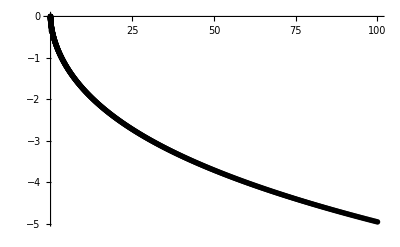

```mathematica
ListPlot[EtaTablenew2]
```

```mathematica
Etafun=Interpolation[EtaTablenew2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
abar=N[((π 2^(-(3/2)))/(Gamma[5/4]Gamma[1/2]))^2]
```

0.477989

```mathematica
etazerofun[ϵ_]:= -abar*√ϵ +(3 π)/32 (Gamma[-3/2]/Gamma[7/2])ϵ^2;
```

```mathematica
Fit[EtaTablenew2,{ϵ^(1/2),ϵ,ϵ^(3/2),ϵ^2},ϵ]
```

-0.499241 √ϵ-0.0331455 ϵ+0.00622615 ϵ^(3/2)-0.000289472 ϵ^2

```mathematica
Etafunnew[ϵ_]:=-0.499241123607184 √ϵ-0.03314548927752185 ϵ+0.006226149365897039 ϵ^(3/2)-0.0002894723806836338 ϵ^2;
```

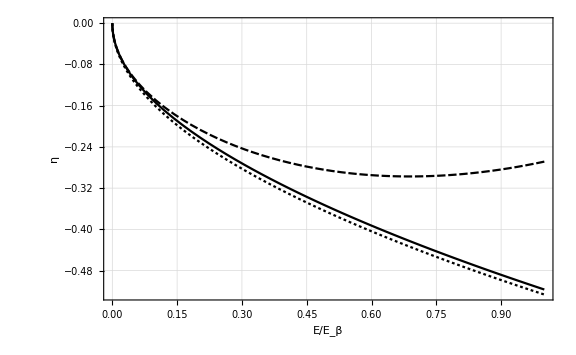

```mathematica
Plot[{Etafun[ϵ],etazerofun[ϵ],Etafunnew[ϵ]},{ϵ,0,1},Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","η"},LabelStyle->Large,
ImageSize->Large]
```

s

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
```

```mathematica
ATable=Table[{EGrid[[ii]],CalcA[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
AOneHalfzero[ϵ_]:= -(abar √ϵ)^(1/2);
```

```mathematica
AOneHalfTable = Table[{ATable[[ii,1]],-√(ATable[[ii,2]])},{ii,1,Length[ATable]}];
```

```mathematica
Fit[AOneHalfTable,{ϵ^(1/4),ϵ^(1/2),ϵ^(3/4),ϵ},ϵ]
```

-0.707259 ϵ^(1/4)-0.0136203 √ϵ+0.0992574 ϵ^(3/4)-0.0177717 ϵ

```mathematica
AOneHalfnew[ϵ_]:=-0.7072588310249918 ϵ^(1/4)-0.013620293154239571 √ϵ+0.09925738445541828 ϵ^(3/4)-0.017771679113266204 ϵ
```

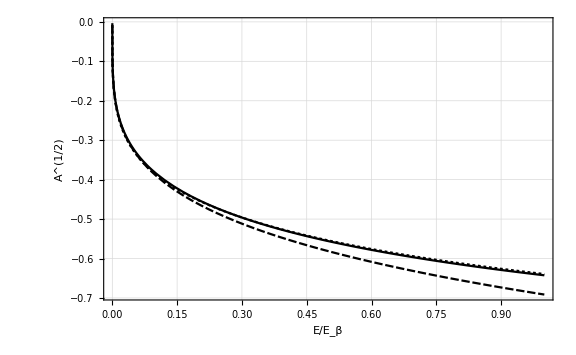

```mathematica
Plot[{-√(Afun[ϵ]),AOneHalfzero[ϵ],AOneHalfnew[ϵ]},{ϵ,0,1},Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","A^(1/2)"},LabelStyle->Large,ImageSize->Large,PlotRange->{0,-1.0}]
```

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
```

```mathematica
GTable=Table[{EGrid[[ii]],CalcG[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Gfun =Interpolation[GTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Gzero[ϵ_]:= (-abar^2+1/3)ϵ;
```

```mathematica
Fit[GTable[[1;;100]],{ϵ,ϵ^2,ϵ^3,ϵ^4},ϵ]
```

0.102209 ϵ-0.0725551 ϵ^2+0.0520161 ϵ^3-0.0201917 ϵ^4

```mathematica
Gnewfun[ϵ_]:=0.10220914744092585 ϵ-0.07255505542391834 ϵ^2+0.05201607591749957 ϵ^3-0.020191680437796247 ϵ^4;
```

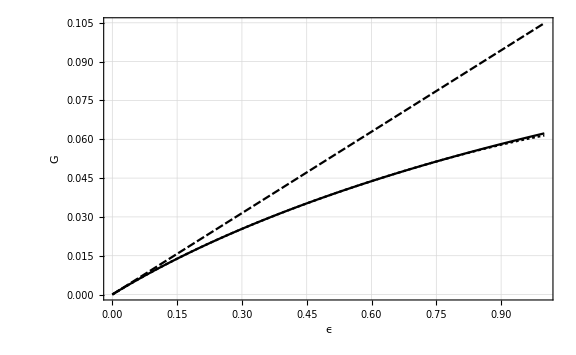

```mathematica
Plot[{Gfun[ϵ],Gzero[ϵ],Gnewfun[ϵ]},{ϵ,0,1.0},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","G"},LabelStyle->Large,ImageSize->Large]
```

```mathematica
Etest =10^-3;
KFTEITable = Table[{bgrid[[ii]], Sqrt[Afun[Etest]] (KtildeFTEI[bgrid[[ii]],Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]]},{ii,1,bn+1}];
```

```mathematica
KFTEITableNew = Table[{bgrid[[ii]], AOneHalfC6[Etest](KtildeFTEINew[bgrid[[ii]],Etest]^-1+GC6[Etest])^-1 AOneHalfC6[Etest]},{ii,1,bn+1}];
(*KFTEITableZero = Table[{bgrid[[ii]], AOneHalfzero[Etest](KtildeFTEIZero[bgrid[[ii]],Etest]^-1+Gzero[Etest])^-1 AOneHalfzero[Etest]},{ii,1,bn+1}];*)
```

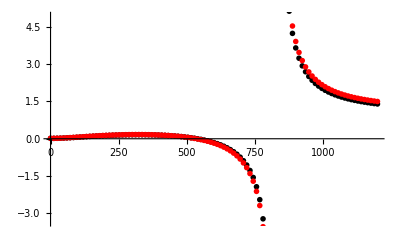

```mathematica
ListPlot[{KFTEITable,KFTEITableNew(*,KFTEITableZero*)},PlotStyle->{Black,Red,Blue}]
```

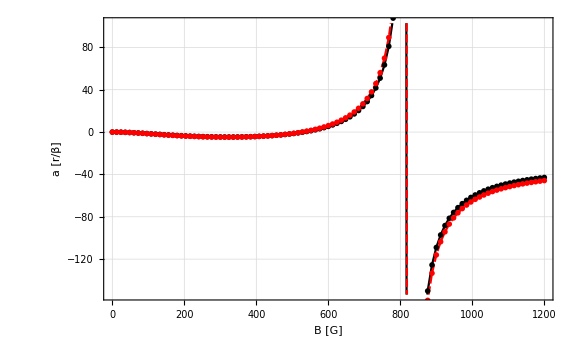

```mathematica
SFTEITable= Table[Exp[ⅈ Etafun[Etest]] ((1+ⅈ KFTEITable[[ii,2]])/(1-ⅈ KFTEITable[[ii,2]])) Exp[ⅈ Etafun[Etest]],{ii,1,bn+1}];
ascatFTEITable=Table[{bgrid[[ii]],Re[-1/(ⅈ Sqrt[Etest]) ((SFTEITable[[ii]]-1)/(SFTEITable[[ii]]+1))]},{ii,1,bn+1}];
SFTEITableNew= Table[Exp[ⅈ EtaC6[Etest]] ((1+ⅈ KFTEITableNew[[ii,2]])/(1-ⅈ KFTEITableNew[[ii,2]])) Exp[ⅈ EtaC6[Etest]],{ii,1,bn+1}];
ascatFTEITableNew=Table[{bgrid[[ii]],Re[-1/(ⅈ Sqrt[Etest]) ((SFTEITableNew[[ii]]-1)/(SFTEITableNew[[ii]]+1))]},{ii,1,bn+1}];
(*SFTEITableZero= Table[Exp[ⅈ etazerofun[Etest]] ((1+ⅈ KFTEITableZero[[ii,2]])/(1-ⅈ KFTEITableZero[[ii,2]])) Exp[ⅈ etazerofun[Etest]],{ii,1,bn+1}];
ascatFTEITableZero=Table[{bgrid[[ii]],Re[-1/(ⅈ Sqrt[Etest]) ((SFTEITableZero[[ii]]-1)/(SFTEITableZero[[ii]]+1))]},{ii,1,bn+1}];*)
ListPlot[{ascatFTEITable,ascatFTEITableNew(*,ascatFTEITableZero*)},Frame->True,FrameLabel->{"B [G]", "a [r/β]"},GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,PlotStyle->{Black,Red,Blue}]
```

```mathematica
logderdat = Import["/Users/alysonlaskowski/LiScattering/Li6FR.dat"];
```

```mathematica
p8=ListPlot[Table[{logderdat[[ii,1]],logderdat[[ii,2]]*BohrinLi6vdw},{ii,1,Length[logderdat]}],PlotStyle->Blue,Joined->True];
```

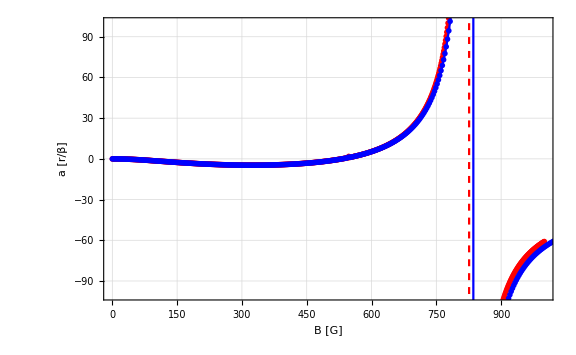

```mathematica
Show[p7,p8]
```

```mathematica
KFTEnergyfun[B_,Ε_]:= Sqrt[Afun[Ε]] (KtildeFTEI[B,Ε]^-1+Gfun[Ε])^-1 Sqrt[Afun[Ε]];
SFTEnergyfun[B_,Ε_]:= Exp[ⅈ Etafun[Ε]] ((1+ⅈ KFTEnergyfun[B,Ε])/(1-ⅈ KFTEnergyfun[B,Ε])) Exp[ⅈ Etafun[Ε]];
```

```mathematica
KFTEnergyfunNew[B_,Ε_]:= AOneHalfC6[Ε] (KtildeFTEINew[B,Ε]^-1+GC6[Ε])^-1 AOneHalfC6[Ε];
SFTEnergyfunNew[B_,Ε_]:= Exp[ⅈ EtaC6[Ε]] ((1+ⅈ KFTEnergyfunNew[B,Ε])/(1-ⅈ KFTEnergyfunNew[B,Ε])) Exp[ⅈ EtaC6[Ε]];
```

```mathematica
kcotdeltaEnergyTable = Table[{Etest,Re[ⅈ ((SFTEnergyfun[200,Etest]+1)/(SFTEnergyfun[200,Etest]-1)) Sqrt[Etest]]},{Etest,10^-4,10^-1,10^-3}];
```

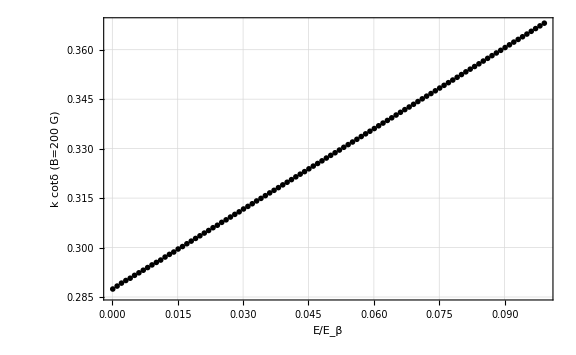

```mathematica
ListPlot[kcotdeltaEnergyTable,Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","k cotδ (B=200 G)"},ImageSize->Large,LabelStyle->Large]
```

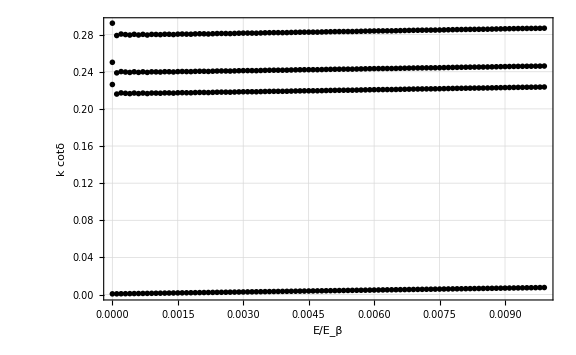

```mathematica
ListPlot[{Table[{Etest,Re[ⅈ ((SFTEnergyfun[200,Etest]+1)/(SFTEnergyfun[200,Etest]-1)) Sqrt[Etest]]},{Etest,10^-6,10^-2,10^-4}],Table[{Etest,Re[ⅈ ((SFTEnergyfun[300,Etest]+1)/(SFTEnergyfun[300,Etest]-1)) Sqrt[Etest]]},{Etest,10^-6,10^-2,10^-4}],Table[{Etest,Re[ⅈ ((SFTEnergyfun[400,Etest]+1)/(SFTEnergyfun[400,Etest]-1)) Sqrt[Etest]]},{Etest,10^-6,10^-2,10^-4}],Table[{Etest,Re[ⅈ ((SFTEnergyfun[837,Etest]+1)/(SFTEnergyfun[837,Etest]-1)) Sqrt[Etest]]},{Etest,10^-6,10^-2,10^-4}]},Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","k cotδ"},ImageSize->Large,LabelStyle->Large]
```

```mathematica
cotdeltafun[Ε_,B_]:=(1-Tan[Etafun[Ε]]KFTEnergyfun[B,Ε])/(Tan[Etafun[Ε]]+KFTEnergyfun[B,Ε]);
```

```mathematica
cotdeltafunNew[Ε_,B_]:=(1-Tan[EtaC6[Ε]]KFTEnergyfunNew[B,Ε])/(Tan[EtaC6[Ε]]+KFTEnergyfunNew[B,Ε]);
```

```mathematica
CalcERE[ΕMin_,ΕMax_,Btest_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{ Εtest,√Εtest cotdeltafun[Εtest,Btest]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
{ascat,reff,EREData}=CalcERE[10^-6,10^-3,200]
```

{-3.51415,-10.6341,{{1/1000000,0.293191},{1009/10000000,0.279825},{251/1250000,0.281455},{3007/10000000,0.280872},{2003/5000000,0.280378},{1001/2000000,0.281173},{1501/2500000,0.280409},{7003/10000000,0.281115},{4001/5000000,0.280397},{9001/10000000,0.281097},{1/1000,0.281019}}}

```mathematica
mqdtnarrowres =Table[{B, CalcERE[10^-4,10^-3,B][[1]]},{B,540,560,0.001}];
```

```mathematica
mqdtwideres = Table[{B, CalcERE[10^-4,10^-3,B][[1]]},{B,0,1000,1.5}];
```

```mathematica
MatrixForm[KsrFTEIQQ[Btest]+CotGammaMatrix[Btest,Etest]]
```

(43.6315 | -10.0131 | -31.4762 | -4.8919
-10.0131 | 15.8975 | -3.7716 | 23.0247
-31.4762 | -3.7716 | 36.1909 | -8.77137
-4.8919 | 23.0247 | -8.77137 | 59.1628)

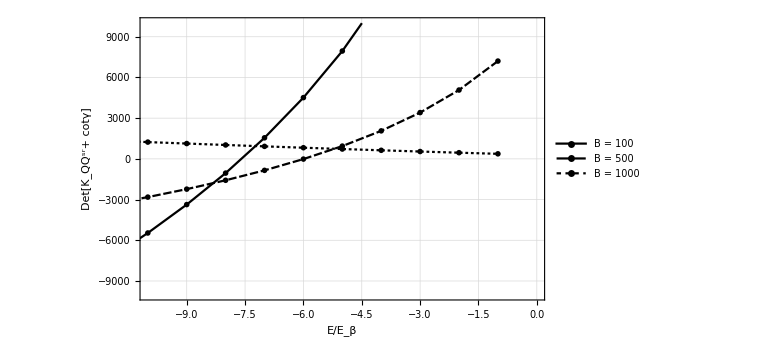

```mathematica
ListLinePlot[{Table[{Etest,Det[KsrFTEIQQ[100]+CotGammaMatrix[100,Etest]]},{Etest,-50,-10^-3,1}],Table[{Etest,Det[KsrFTEIQQ[200]+CotGammaMatrix[200,Etest]]},{Etest,-50,-10^-3,1}],Table[{Etest,Det[KsrFTEIQQ[1000]+CotGammaMatrix[1000,Etest]]},{Etest,-50,-10^-3,1}]},Frame->True,GridLines->Automatic,FrameLabel->{"E/E_β","Det[K_QQ^sr+ cotγ]"},ImageSize->Large,LabelStyle->Large,PlotLegends->{"B = 100","B = 500", "B = 1000"},PlotRange->{{-10,0},{-10000,10000}}]
```

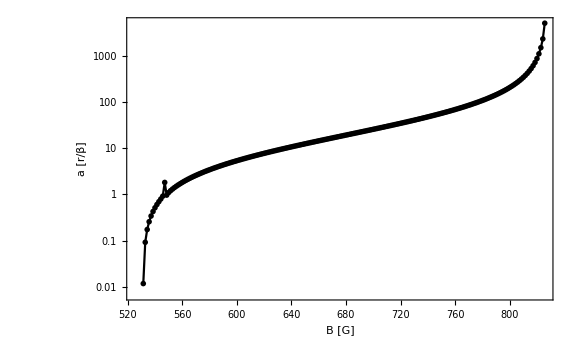

```mathematica
ListLogPlot[ascatFTEITable2,Frame->True,FrameLabel->{"B [G]", "a [r/β]"},GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,PlotRange->Full]
```

```mathematica
Length[logderdat]
```

400

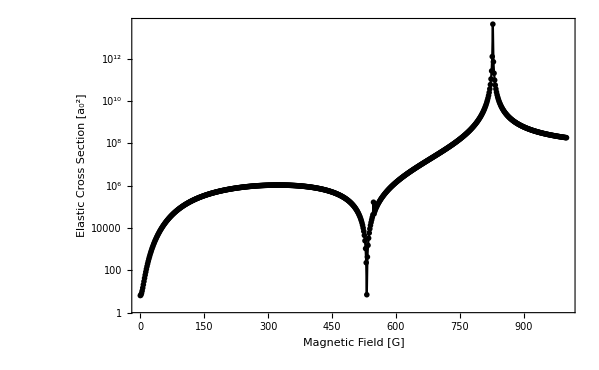

```mathematica
ListLogPlot[{Table[{bgrid2[[ii]],4π(ascatFTEITable2[[ii,2]]*1/BohrinLi6vdw)^2},{ii,1,bn2+1}](*,Table[{logderdat[[ii,1]],4π (logderdat[[ii,2]])^2},{ii,1,340}]*)},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Black,Red}]
```

```mathematica
Li6HVDW[r_,B_]= Li6HZVDW[B]+Triplet6Proj*ALi6VDW[r]+Singlet6Proj*XLi6VDW[r];
```

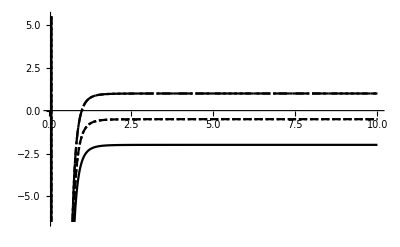

```mathematica
Plot[{Li6HVDW[r,0][[1,1]],Li6HVDW[r,0][[2,2]],Li6HVDW[r,0][[3,3]],Li6HVDW[r,0][[4,4]],Li6HVDW[r,0][[5,5]]},{r,0.05,10}]
```

```mathematica
H6rotated[r_,B_]:= Transpose[DD[B]].Li6HVDW[r,B].DD[B]
```

```mathematica
Plot[{H6rotated[r,0][[1,1]],H6rotated[r,0][[2,2]],H6rotated[r,0][[3,3]],H6rotated[r,0][[4,4]],H6rotated[r,0][[5,5]]},{r,0.05,10}]
```

-Graphics-

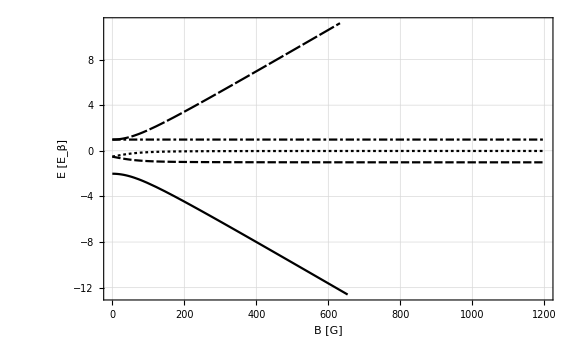

```mathematica
Plot[{H6rotated[2,B][[1,1]],H6rotated[2,B][[2,2]],H6rotated[2,B][[3,3]],H6rotated[2,B][[4,4]],H6rotated[2,B][[5,5]]},{B,0,1200},GridLines->Automatic,Frame->True,ImageSize->Large,FrameLabel->{"B [G]","E [E_β]"},LabelStyle->Large]
```

```mathematica
ascatfun[B_,Ε_]:= -1/(Sqrt[Ε] cotdeltafun[Ε,B]);
```

```mathematica
ascatfunNew[B_,Ε_]:= -1/(Sqrt[Ε] cotdeltafunNew[Ε,B]);
```

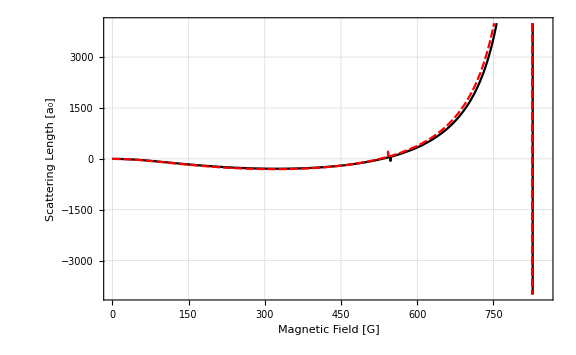

```mathematica
Plot[{ascatfun[B,Etest]/BohrinLi6vdw,ascatfunNew[B,Etest]/BohrinLi6vdw},{B,0,850},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Scattering Length [a_0]" },PlotStyle->{Black,Red},PlotRange->{{0,850},{-4000,4000}}]
```

```mathematica
ascat[B_]:= ascatfun[B,Etest];
```

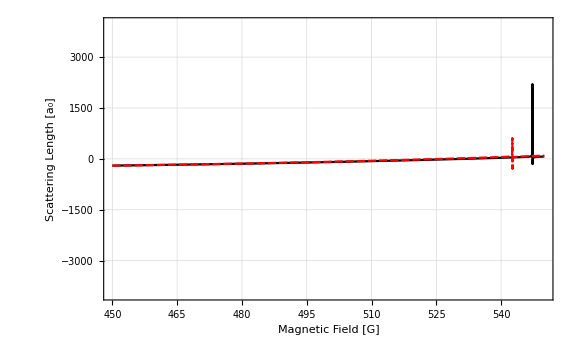

```mathematica
Plot[{ascatfun[B,Etest]/BohrinLi6vdw,ascatfunNew[B,Etest]/BohrinLi6vdw},{B,450,550},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Scattering Length [a_0]" },PlotStyle->{Black,Red},PlotRange->{{450,550},{-4000,4000}}]
```

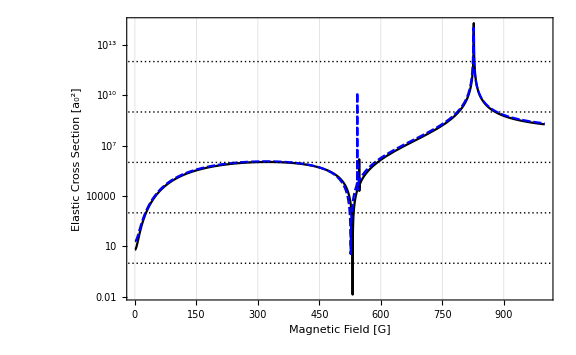

```mathematica
pmqdt =LogPlot[{4π(ascatfun[B,Etest]/BohrinLi6vdw)^2,4π(ascatfunNew[B,Etest]/BohrinLi6vdw)^2},{B,0,1000},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Black,Blue}]
```

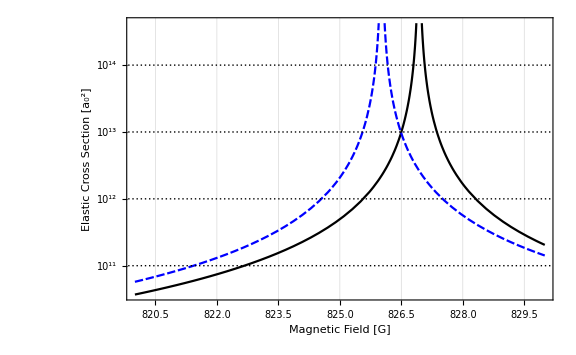

```mathematica
pmqdt =LogPlot[{4π(ascatfun[B,Etest]/BohrinLi6vdw)^2,4π(ascatfunNew[B,Etest]/BohrinLi6vdw)^2},{B,820,830},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Black,Blue}]
```

Log-derivative Data:

```mathematica
narrowresdat = Import["/Users/alysonlaskowski/LiScattering-Li6/Li6FR.dat"];
```

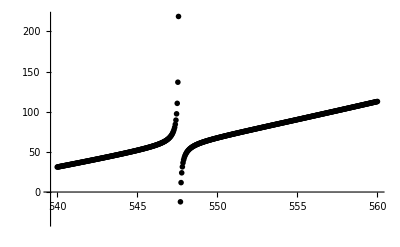

```mathematica
ListPlot[narrowresdat]
```

```mathematica
wideresdat =  Import["/Users/alysonlaskowski/LiScattering-Li6/Li6FR.dat"];
```

```mathematica
logderdat = Flatten[{narrowresdat,wideresdat},1];
logderdat[[Length[logderdat]]]
```

{1000.,-4079.61}

```mathematica
logderdatnew = Sort[logderdat];
```

```mathematica
logderdatnew[[Length[logderdatnew]]]
```

{1000.,-4079.61}

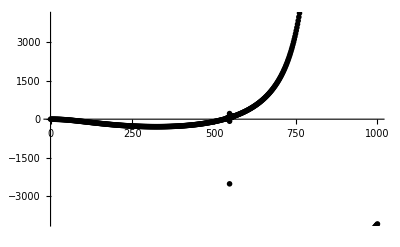

```mathematica
ListPlot[logderdatnew,PlotRange->{{0,1000},{-4000,4000}}]
```

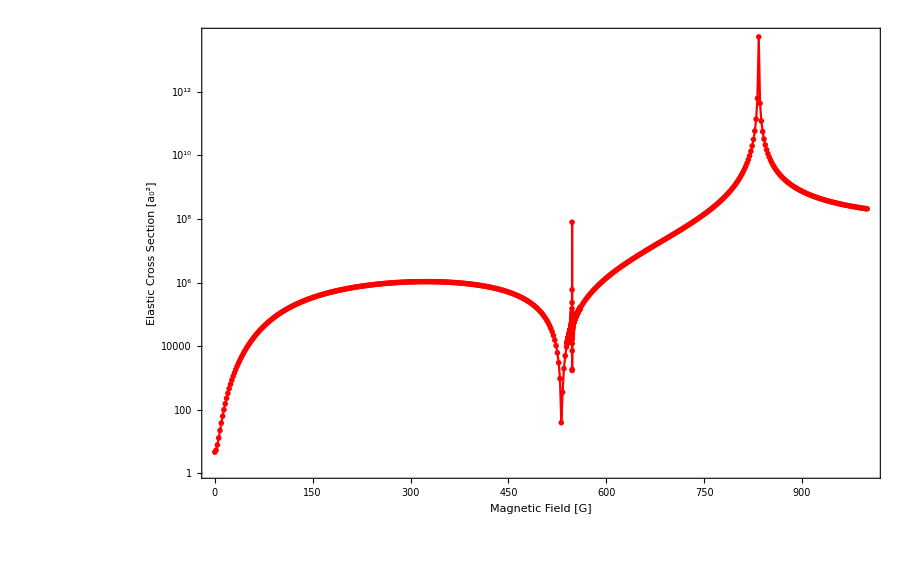

```mathematica
p10 =ListLogPlot[ Table[{logderdatnew[[ii,1]],4π (logderdatnew[[ii,2]])^2},{ii,1,Length[logderdatnew]}],Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Red}]
```

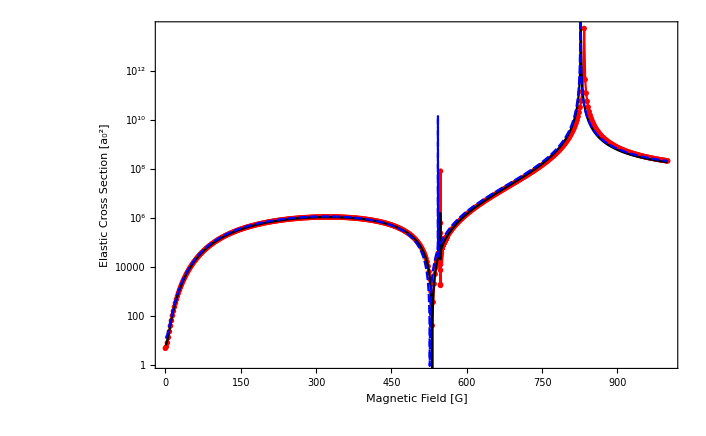

```mathematica
Show[p10,pmqdt]
```